```mathematica
Needs["FeynArts`"]
Needs["FormCalc`"]
```

FeynArts 3.11 (25 Mar 2022)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

FormCalc 9.9 (11 Dec 2021)

by Thomas Hahn

```mathematica
CKM = IndexDelta;
Neglect[ME] = Neglect[ME2] = 0;
$FAVerbose=1;
SetOptions[InsertFields, Model -> ToFileName[$HomeDirectory,"DM-EFT/ModelFiles-sms/SMS-top_FA/SMS-top_FA"],GenericModel->ToFileName[$HomeDirectory,"DM-EFT/ModelFiles-sms/SMS-top_FA/SMS-top_FA"],ExcludeParticles->{S[1]}];
SetOptions[Paint, PaintLevel -> {Classes}];
```

```mathematica
processSMEFT = { V[4],V[4]} -> {-F[9], F[9]};
nameSMEFT = "SM-EFT";
topsSMEFT = CreateTopologies[1, 2-> 2,  ExcludeTopologies -> {TadpoleCTs,Tadpoles, WFCorrectionCTs,SelfEnergies,SelfEnergyCTs}];
insSMEFT = InsertFields[topsSMEFT, processSMEFT,InsertionLevel-> Particles,LastSelections->{S[4]}];
```

in total: 7 Generic, 7 Classes, 7 Particles insertions

```mathematica
processDMEFT = { V[4],V[4]} -> {S[4],S[4]};
nameDMEFT = "DM-EFT";
topsDMEFT = CreateTopologies[1, 2->2,  ExcludeTopologies -> {TadpoleCTs,Tadpoles, WFCorrectionCTs,SelfEnergies,SelfEnergyCTs}];
insDMEFT = InsertFields[topsDMEFT, processDMEFT,InsertionLevel-> Particles];
```

in total: 4 Generic, 16 Classes, 16 Particles insertions

```mathematica
processSMS = { V[4],V[4]} -> {-F[9], F[9],S[4],S[4]};
nameSMS = "SMS";
topsSMS = CreateTopologies[0, 2-> 4,  ExcludeTopologies -> {TadpoleCTs,Tadpoles, WFCorrectionCTs,SelfEnergies,SelfEnergyCTs}];
insSMS = InsertFields[topsSMS, processSMS,InsertionLevel-> Particles];
```

in total: 30 Generic, 30 Classes, 30 Particles insertions

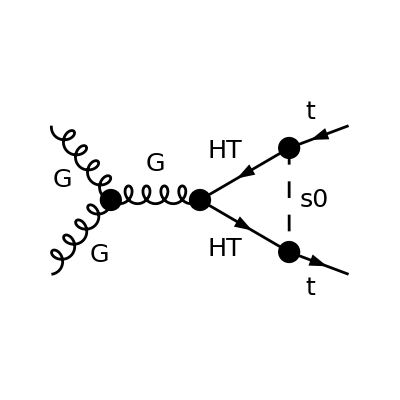

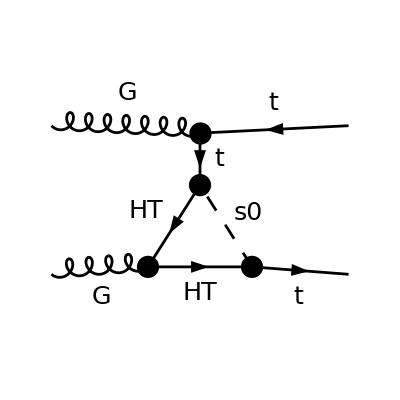

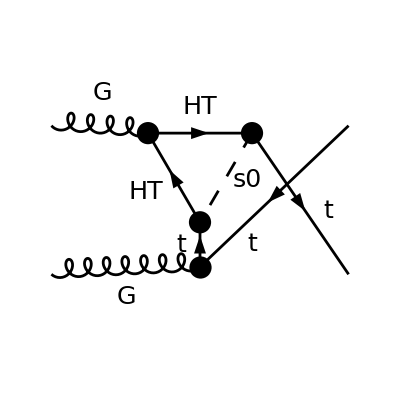

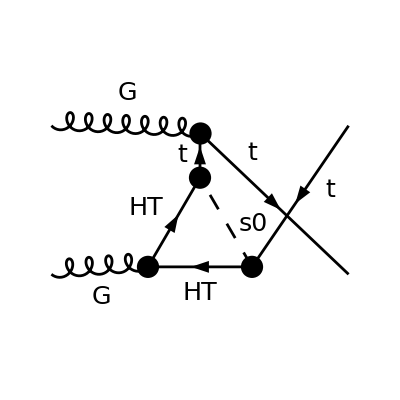

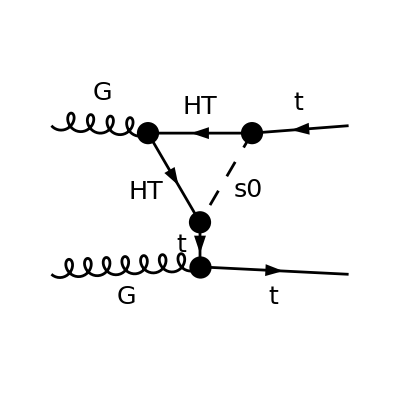

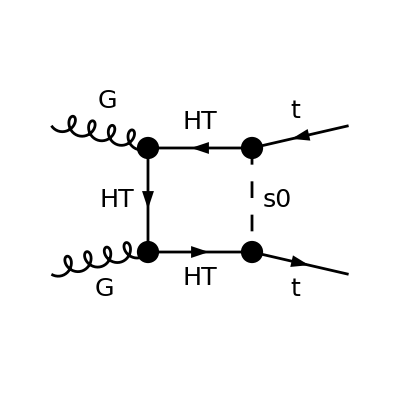

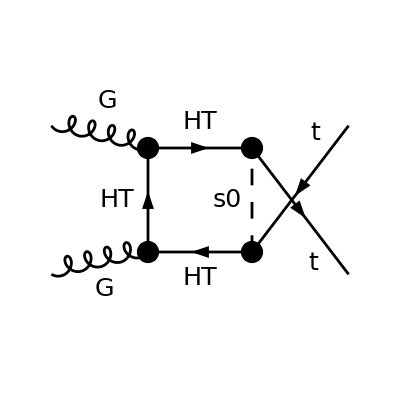

FeynArtsGraphics[SM-EFT][([]),([]),([]),([]),([]),([]),([])]

```mathematica
Paint[insSMEFT,ColumnsXRows->1,PaintLevel->{Classes},SheetHeader->nameSMEFT,Numbering->None,AutoEdit->True]
```

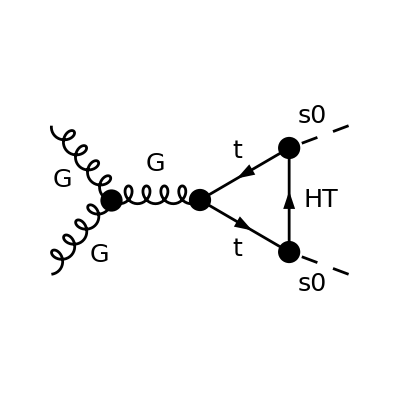

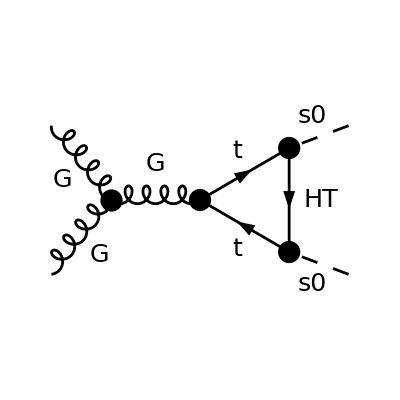

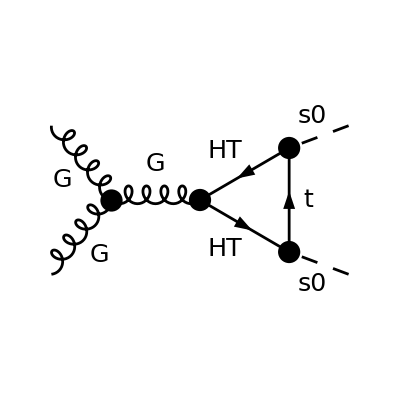

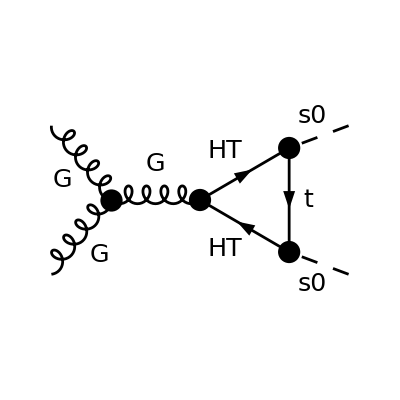

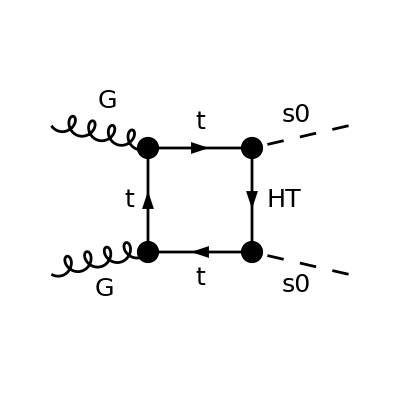

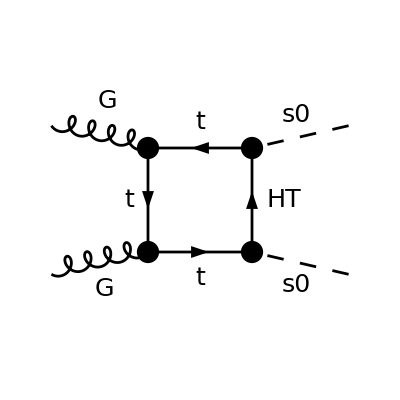

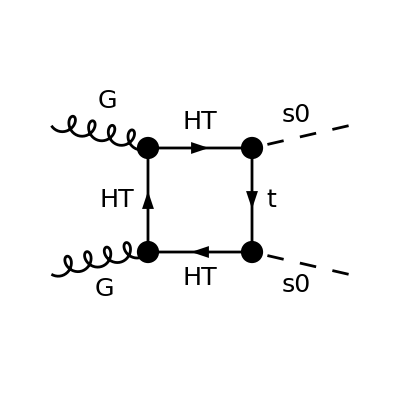

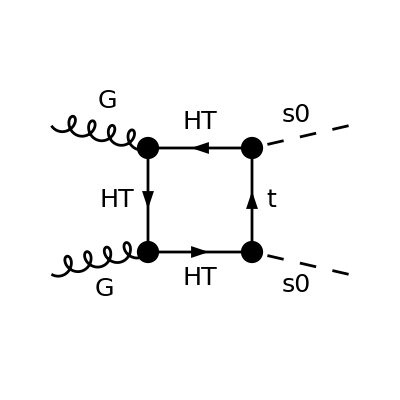

FeynArtsGraphics[DM-EFT][([]),([]),([]),([]),([]),([]),([]),([]),([]),([]),([]),([]),([]),([]),([]),([])]

```mathematica
Paint[insDMEFT,ColumnsXRows->1,PaintLevel->{Classes},SheetHeader->nameDMEFT,Numbering->None,AutoEdit->True]
```

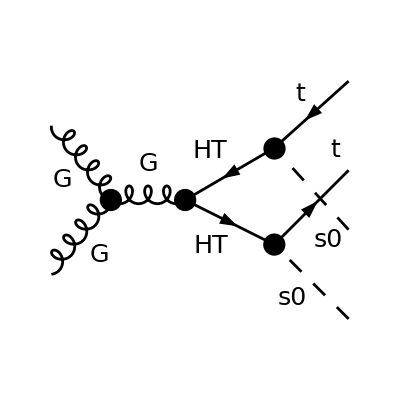

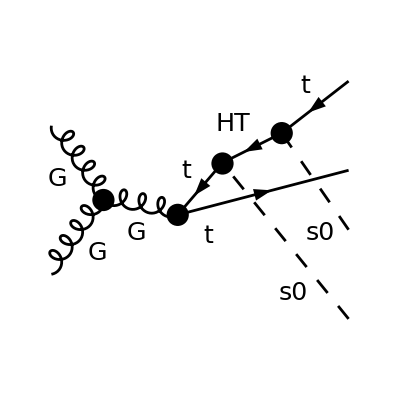

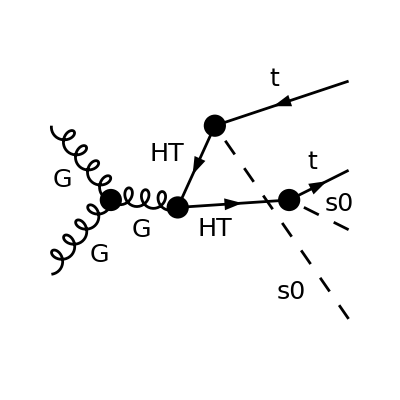

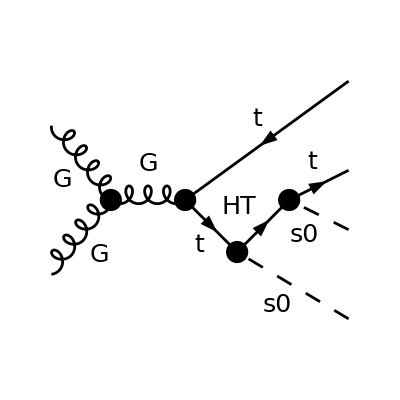

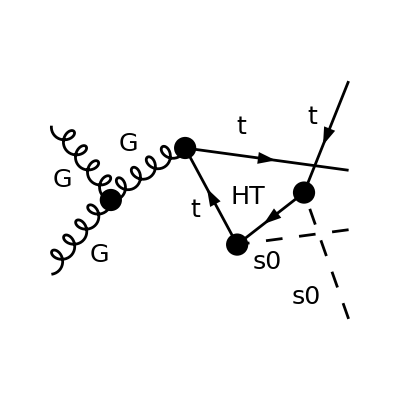

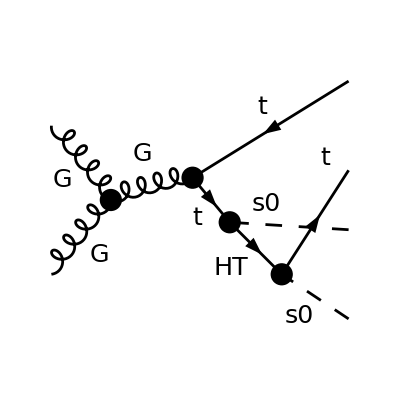

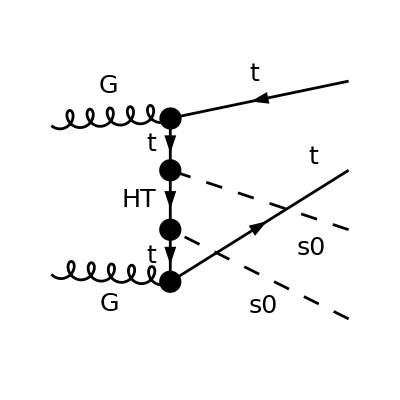

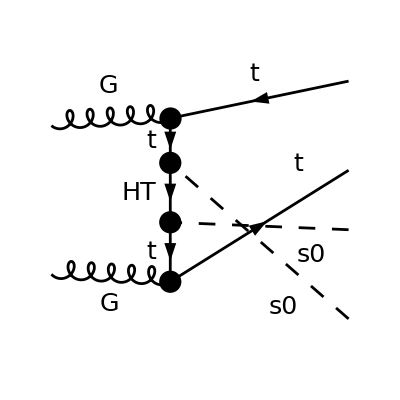

FeynArtsGraphics[SMS][([]),([]),([]),([]),([]),([]),([]),([]),([]),([]),([]),([]),([]),([]),([]),([]),([]),([]),([]),([]),([]),([]),([]),([]),([]),([]),([]),([]),([]),([])]

```mathematica
Paint[insSMS,ColumnsXRows->1,PaintLevel->{Classes},SheetHeader->nameSMS,Numbering->None,AutoEdit->True]
```